# parton.note.1.nb

```mathematica
NotebookFileName[]
```

D:\gitstorage\note\parton-df\parton.note.1.nb

## notation

k^+→k`p, k^-→k`m,k_⊥=k`perp,

Ω_ϕ→Ω`ϕ

baryon→ba

mesons→ϕ

## definition

d`ϕ[k_]:=k^2-(m`ϕ)^2+I ϵ==k`p*k`m-k`perp-(m`ϕ)^2+I ϵ==k`p*k`m-Ω`ϕ+I ϵ

d`ba[k_]:=(p-k)^2-(m`ba)^2+I ϵ==(p-k)`p*(p-k)`m-k`perp-(m`ba)^2+I ϵ==(p-k)`p*(p-k)`m-(Ω`ba)^2+I ϵ

Ω`ϕ:=(k`perp)^2+(m`ϕ)^2≥0

Ω`ba:=(k`perp)^2+(m`ba)^2≥0

k`p*k`m-(k`perp)^2=(m`ϕ)^2

p`p*p`m-(p`perp=0)^2=(m`ba)^2

## calc`1

```mathematica
mass`rule={
Ω`ϕ->(k`perp)^2+(m`ϕ)^2,Ω`ba->(k`perp)^2+(m`ba)^2,
k`p->y*p`p,p`m->(m`ba)^2/p`p
};
```

```mathematica
(
(
(p`p-k`p)*k`p*((p`m-(Ω`ϕ)/(k`p))-(Ω`ba)/(p`p-k`p))
)//.mass`rule
)//Simplify
```

-p`p ((k`perp)^2+(m`ba)^2 y^2-(-1+y) (m`ϕ)^2)

## calc`2

(∫^∞)_(-∞)ⅆk`m 1/(D`ϕ)==(∫^∞)_(-∞)ⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ)

Simplify notation a little

((∫ⅆz)^∞)_(-∞)1/(z-a+I ϵ),a≥0

## if k`p > 0

单极点在 1/(k`p)(Ω_ϕ-I ϵ),(第四象限), 做一个顺时针的闭合回路，积分共有两部分，利用留数定理。

ParametricPlot[{{Cos[t],Sin[t]},{(2(t-3π/2))/π,0}},{t,π,2π}]

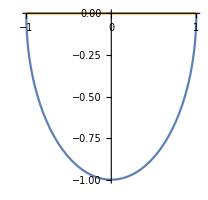

int+(∫_0)^-π(I R e^(I φ) ⅆφ)/(R e^(I φ)-a+I ϵ)+→

int+(∫_0)^(-π/2)(I R e^(I φ) ⅆφ)/(R e^(I φ)-a)=-2π I *(1)

```mathematica
int`b=Assuming[{R>a>ϵ>0},
Simplify[Integrate[I R Exp[I φ]/(R Exp[I φ]-a+I ϵ),{φ,0,-π}]]
]
```

-ⅈ π+2 ArcTanh[(a-ⅈ ϵ)/R]

## add and simplify

```mathematica
int`b`simlif=Assuming[{R>a>0},
Limit[int`b,ϵ->0,Direction->"FromAbove"]
]//Simplify
```

-ⅈ π+2 ArcTanh[a/R]

```mathematica
int`result=Assuming[{R>a>0},
(-2π I-int`b`simlif)/.{a->li*R}//Simplify
]
```

-ⅈ π-2 ArcTanh[li]

so,

int`result→-ⅈ π-2 ArcTanh[li]→(R→+∞,a/R→0)→-ⅈ π

## apply

∫ⅆk`m 1/(D`ϕ)==∫ⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ),

∫ⅆz/(z-a+I ϵ)==-ⅈ π,a≥0

******************************************

∫ⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ)→

if y≠0, then

→1/(k`p)∫ⅆ(k`p*k`m)1/(k`p*k`m-Ω`ϕ+I ϵ)→1/(k`p)∫ⅆz 1/(z-Ω`ϕ+I ϵ)→

1/(k`p)(-ⅈ π)→(-ⅈ π)1/y 1/(p`p)

## if k`p = 0

(∫^∞)_(-∞)ⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ)→1/(-Ω`ϕ+I ϵ)(∫^∞)_(-∞)ⅆk`m→∞ (k`p=0)

## if k`p < 0

单极点在 1/(k`p)(Ω_ϕ-I ϵ)(第二象限), 做一个顺时针的闭合回路，积分共有两部分，利用留数定理。

积分回路中不包含极点，所以和为0

ParametricPlot[{{Cos[t],Sin[t]},{(2(t-3π/2))/π,0}},{t,π,2π}]

-Graphics-

int+(∫_0)^-π(I R e^(I φ) ⅆφ)/(R e^(I φ)-a+I ϵ)+→

int+(∫_0)^(-π/2)(I R e^(I φ) ⅆφ)/(R e^(I φ)-a)=0

so,

1/(k`p)∫ⅆ(k`p*k`m)1/(k`p*k`m-Ω`ϕ+I ϵ)==-1/(k`p)(∫_0)^-π arc==-1/(k`p)(-ⅈ π)==1/(k`p)ⅈ π

**************************************************

conclusion

1/(k`p)∫ⅆ(k`p*k`m)1/(k`p*k`m-Ω`ϕ+I ϵ)

k`p*k`m-Ω`ϕ+I ϵ, can be written as,

k`p*(k`m-(Ω`ϕ-I ϵ)/(k`p)),

********************

k`p>0,

(k`p+I δ Ω`ϕ)(k`m-((Ω`ϕ)/(k`p)-I k`p δ))→第四象限

k`p k`m -Ω`ϕ+ⅈ δ((k`p)^2 +  (Ω`ϕ)/(k`p)(k`p k`m- Ω`ϕ))

k`p k`m- Ω`ϕ==k^2-(m`ϕ)^2+I ϵ≥0, 在积分之后,写成费曼截面的时候,总是正的--on shell

so,ⅈ δ((k`p)^2 +  (Ω`ϕ)/(k`p)(k`p k`m- Ω`ϕ))always positive, can be noted as ⅈ ϵ,

k`p k`m -Ω`ϕ+ⅈ δ((k`p)^2 +  (Ω`ϕ)/(k`p)(k`p k`m- Ω`ϕ))→k`p k`m -Ω`ϕ+ⅈ ϵ

**************************************

k`p<0,

(k`p-I δ Ω`ϕ)(k`m-((Ω`ϕ)/(k`p)-I k`p δ))→第二象限

k`m k`p-Ω`ϕ+ⅈ δ((k`p)^2 - (Ω`ϕ)/(k`p)(k`p k`m  - Ω`ϕ))

ⅈ δ((k`p)^2 - (Ω`ϕ)/(k`p)(k`p k`m  - Ω`ϕ)) always positive ,can be noted as ⅈ ϵ,

k`p k`m -Ω`ϕ+ⅈ δ((k`p)^2 - (Ω`ϕ)/(k`p)(k`p k`m  - Ω`ϕ))→k`p k`m -Ω`ϕ+ⅈ ϵ

****************************************

1/(k`p)∫ⅆ(k`p*k`m)1/(k`p*k`m-Ω`ϕ+I ϵ)→ (-ⅈ π θ[k`p])/(k`p+I δ Ω`ϕ)+(ⅈ π θ[-k`p])/(k`p-I δ Ω`ϕ),δ→0

其中θ[k`p]是阶跃函数

*********************

## another side

∫ⅆk`pⅆk`m 1/(k`p*k`m-Ω`ϕ+I ϵ)^2

```mathematica
Integrate[1/(k`p*k`m-Ω`ϕ)^2,{k`m,-∞,∞},{k`p,-∞,∞},PrincipalValue->True]
```

Integrate::idiv: 1/(-k`m k`p+Ω`ϕ)^2 的积分在 {-∞,∞} 上不收敛.